```mathematica
(* Mathematica simulation of geofence inclusion algorithm / methods *)
Needs["Polytopes`"];
```

```mathematica
polygon=Vertices[Dodecagon];
```

```mathematica
𝒫=RandomPolygon[7]
polygon=PolygonCoordinates[CanonicalizePolygon[𝒫]]
```

Polygon[…]

{{0.00661238,0.0898943},{0.160287,0.937344},{0.200135,0.936559},{0.357186,0.714043},{0.733297,0.165603},{0.87604,0.839228},{0.911588,0.161169}}

```mathematica
lines=MapThread[{#1, #2}&, {polygon, Append[polygon[[2;;]], First[polygon]]}]
```

{{{0.00661238,0.0898943},{0.160287,0.937344}},{{0.160287,0.937344},{0.200135,0.936559}},{{0.200135,0.936559},{0.357186,0.714043}},{{0.357186,0.714043},{0.733297,0.165603}},{{0.733297,0.165603},{0.87604,0.839228}},{{0.87604,0.839228},{0.911588,0.161169}},{{0.911588,0.161169},{0.00661238,0.0898943}}}

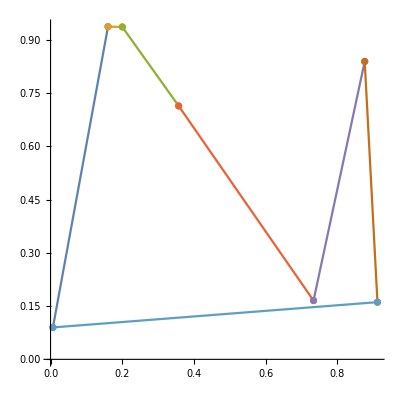

```mathematica
Show[ListLinePlot[lines, {AspectRatio->1, PlotLegends->"Expressions"}], ListPlot[lines]]
```

```mathematica
SimplePolygonQ[Polygon[#[[1]]&/@lines]]
```

True

```mathematica
(*
Determine if clockwise/counterclockwise.
	@param lat-forecasted latitude of gps coordinate
	@param lon-forecasted longitude of gps coordinate
	@param q geofence perimeter coordinate i
	@param r geofence perimeter coordinate i+1
	@return-true: Counterclockwise (left side of gps/q),false if not
*)
ccw[lat_, lon_, q_, r_]:= Module[{vectorGpsQ, vectorGpsR,crossProduct},
vectorGpsQ=q-{lon,lat};
vectorGpsR=r-{lon,lat};
crossProduct=vectorGpsQ[[1]]vectorGpsR[[2]]-vectorGpsQ[[2]]vectorGpsR[[1]];
crossProduct>0
]
```

```mathematica
ccw[0,1,{1,2}, {3,4}]
```

False

```mathematica
(* Calculate the angle between perimeter vector and gps
     @param lat-forecasted latitude of gps coordinate
     @param lon-forecasted longitude of gps coordinate
     @param q geofence perimeter coordinate i
     @param r geofence perimeter coordinate i+1
     @return angle
*)
angle[lat_, lon_,q_,r_]:=Module[{vectorGpsQ, vectorGpsR,normGpsQ, normGpsR,dotProduct}, 
vectorGpsQ=q-{lon, lat};
vectorGpsR=r-{lon,lat};
 dotProduct=vectorGpsQ.vectorGpsR;
 normGpsQ=Norm[vectorGpsQ];
 normGpsR=Norm[vectorGpsR];
If[normGpsQ==0||normGpsR==0,0,ArcCos[dotProduct/(normGpsQ normGpsR)]]
]
```

```mathematica
angle[0, 1, {1,2},{3,4}]
```

ArcCos[2/(√5)]

```mathematica
(*
 Determine is gps is between perimeter points
 @param lat-forecasted latitude of gps coordinate
 @param lon-forecasted longitude of gps coordinate
 @param q geofence perimeter coordinate i
 @param r geofence perimeter coordinate i+1
 @return boolean-true if between,false if not
 *)
 between[ lat_, lon_, q_,r_]:= Module[{EPS=10^-9},
lat<(Max[q[[2]],r[[2]]]+EPS)&&(lat+EPS)>Min[q[[2]],r[[2]]]&&lon<(Max[q[[1]],r[[1]]]+EPS)&&(lon+EPS)>Min[q[[1]],r[[1]]]
]
```

```mathematica
between[4,3.01,{1,2},{3,4}]
```

False

```mathematica
(*
Determine if forecasted drone gps coordinate is within geofence polygon
Reference:https://www.engr.colostate.edu/~dga/documents/papers/point_in_polygon.pdf (Point inclusion-Winding Number Algorithm)
 @param gps-Current drone location
 @return boolean-true:inside geofence perimeter (also failed gps),false:outside geofence perimeter
*)
insideGeofence[location_, geofence_]:= Module[{EPS=10^-9,lat, lon, sum, p1, p2, ang},
lon=location[[1]]; 
lat=location[[2]];
sum=0.;
For[i=0,i<Length[geofence],i++,
p1=geofence[[i+1]];
p2=geofence[[Mod[i+1,Length[geofence]]+1]];
ang=angle[lat,lon,p1,p2];
If [(Abs[ang]<EPS||Abs[ang-π]<EPS)&&between[lat,lon,p1,p2],Return[True](* Angle less than epsilon and gps between perimeter points i & i+1 *)
];
sum+=If[ccw[lat,lon,p1,p2],ang,-ang];
(*If left side of vector from gps& i:sum angle,else right side:subtract angle *)
];
Abs[2 π-Abs[sum]]<EPS
]
```

```mathematica
point={0,1};
insideGeofence[point, polygon]
```

False

```mathematica
(* point to line distance: *)
(*
Calculate distance from point to line.
Helper for calculating nearest point to geofence.
Reference:https://stackoverflow.com/questions/849211/shortest-distance-between-a-point-and-a-line-segment
      @return {distance,yy,xx} where yy,xx are the coordinates of the nearest point on the line,
to our (lat,lon) point.*)
nearestPointToLine[lat_,lon_,p1_,p2_,overshoot_]:= Module[{x1,y1,x2,y2,xx,yy, a, b,c, d, dot, lenSq, param},
 {
x1=p1[[1]];
y1=p1[[2]];
 x2=p2[[1]];
 y2=p2[[2]];
 a=lat-y1;
 b=lon-x1;
 c=y2-y1;
 d=x2-x1;
 dot=a c+b d;
 lenSq=c c+d d;
 param=-1.;
If[lenSq≠0,param=dot/lenSq,{}];

If [param<0,xx=x1;yy=y1,If[param>1 ,xx=x2;yy=y2, xx=x1+param d;yy=y1+param c]];

 dx=xx-lon;
 dy=yy-lat;
(* Overshoot the perimeter point towards the other side of the line *)  theta=If[dx==0&&dy==0,0,ArcTan[dx,dy]];
xx+=overshoot Cos[theta];
yy+=overshoot Sin[theta];
√(dx^2+dy^2),{xx, yy}}]
```

```mathematica
point={0,0};
overshoot=1/10;
```

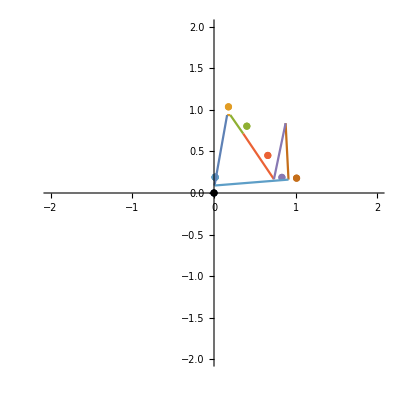

```mathematica
nearest =nearestPointToLine[point[[2]], point[[1]],#[[1]], #[[2]],overshoot]&/@lines//N;
Show[ListPlot[{#[[2]]}&/@nearest, {PlotRange-> {{-2,2},{-2,2}},AspectRatio->1}], ListLinePlot[lines],ListPlot[{Style[point, Black]}]]
```

```mathematica
(* Calculates minimum distance from point to geofence.
Reference:https://stackoverflow.com/questions/10983872/distance-from-a- point-to-a-polygon
   @return Point(yy,xx) where yy,xx are the coordinates of the nearest point on the
   geofence's polygon,to our `location` point.
*)
nearestPointToGeofence[location_, geofence_, overshoot_]:= Module[{lat, lon, minDistance},
 lat=location[[2]];
 lon=location[[1]];
If[insideGeofence[location, geofence], Return[location]];
 minDistance=10^100;
 xx=lon;
 yy=lat;

For[ i=0,i<Length[geofence],i++,
p1=geofence[[i+1]];
p2=geofence[[Mod[(i+1),Length[geofence]]+1]]; minPoint=nearestPointToLine[lat,lon,p1,p2,overshoot];
distance=minPoint[[1]];
If [distance<minDistance, {
minDistance=distance;
xx=minPoint[[2]][[1]];
yy=minPoint[[2]][[2]];
}];
];
{xx, yy}];
```

{0.131511,0.200041}

Inside:False

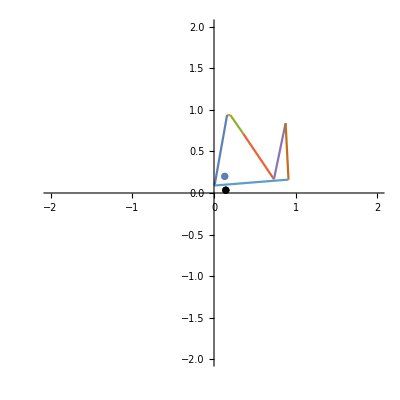

```mathematica
point=RandomPoint[Rectangle[]];
nearestToGeofence=nearestPointToGeofence[point, polygon,1/10]//N
Print["Inside:", insideGeofence[point, polygon]];
Show[ListPlot[{nearestToGeofence}, {PlotRange-> {{-2,2},{-2,2}},AspectRatio->1}], ListLinePlot[lines],ListPlot[{Style[point, Black]}]]
```